# Test Null Student-T Sigma

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_null_ST_sigma.cpp -O3 -o test/NDFs/test_null_ST_sigma"]
```

0

```mathematica
roughness="0.75";
majorant="3";
gamma="2.8";
du=0.01;
```

```mathematica
argstr=roughness<>" "<>majorant<>" "<>gamma<>" "<>ToString[du]<>" > test/NDFs/sigma.txt"
```

0.75 3 2.8 0.01 > test/NDFs/sigma.txt

```mathematica
Run["./test/NDFs/test_null_ST_sigma "<>argstr]
```

256

```mathematica
check=Import["test/NDFs/sigma.txt","Table"];
```

```mathematica
check
```

{{roughness:,0.75},{majorant:,3},{gamma:,2.8},{du:,0.01},{1.08284×10^-6,0.0000802064,0.000256165,0.00051889,0.00085808,0.00127029,0.00175317,0.00230398,0.00291986,0.00359863,0.00434101,0.00514946,0.0060134,0.00693479,0.00792223,0.00896019,0.0100579,0.0112128,0.0124174,0.0136863,0.0149995,0.0163764,0.0177969,0.0192797,0.0208054,0.0223927,0.0240214,0.025712,0.0274423,0.0292345,0.0310668,0.0329572,0.0348932,0.0368777,0.0389158,0.0409941,0.0431318,0.0453075,0.0475394,0.0498172,0.0521374,0.0545142,0.056928,0.0593974,0.0619123,0.0644671,0.0670788,0.069729,0.0724276,0.0751766,0.0779617,0.0808028,0.0836871,0.0866101,0.0895888,0.092607,0.0956681,0.0987819,0.101933,0.105132,0.108379,0.111664,0.114998,0.118379,0.121795,0.125264,0.128777,0.132326,0.135928,0.139573,0.143254,0.146988,0.150764,0.154577,0.158441,0.162348,0.166292,0.170287,0.174324,0.178399,0.182523,0.186691,0.190896,0.195149,0.199447,0.203782,0.208164,0.212591,0.217056,0.221567,0.226122,0.230718,0.235356,0.240041,0.244766,0.249533,0.254345,0.2592,0.264095,0.269036,0.274019,0.279045,0.284112,0.289226,0.294379,0.299575,0.304818,0.3101,0.315424,0.320796,0.326208,0.33166,0.33716,0.342702,0.348284,0.353912,0.359584,0.365295,0.371052,0.376854,0.382695,0.388581,0.394514,0.400484,0.4065,0.412564,0.418664,0.424811,0.431006,0.437237,0.443515,0.449841,0.456204,0.462614,0.469072,0.475566,0.482109,0.488699,0.495327,0.502004,0.508727,0.515487,0.5223,0.529156,0.536051,0.543001,0.549989,0.55702,0.564107,0.571231,0.578401,0.585624,0.592883,0.600196,0.607553,0.614951,0.622406,0.629899,0.637443,0.645036,0.652668,0.660359,0.668088,0.67587,0.683701,0.691573,0.699505,0.707475,0.715503,0.723575,0.731698,0.739872,0.748092,0.75637,0.76469,0.773072,0.781494,0.78998,0.798507,0.807097,0.815731,0.824428,0.833173,0.841976,0.850835,0.859746,0.868721,0.877747,0.886834,0.895984,0.90519,0.914456,0.92379,0.933188,0.942651,0.952182,0.961784,0.971459},{0,0,0,0.00001,0.00011,0.00009,0.00016,0.00023,0.00025,0.0004,0.00044,0.00049,0.00062,0.00081,0.00086,0.0009,0.00104,0.00123,0.00145,0.00176,0.00181,0.0017,0.00194,0.00191,0.00204,0.00216,0.00241,0.00289,0.00299,0.00336,0.00313,0.00326,0.00367,0.00416,0.00432,0.00417,0.00432,0.00462,0.00501,0.0059,0.00531,0.00566,0.00653,0.00642,0.00705,0.00624,0.00674,0.00761,0.00745,0.00808,0.0083,0.00804,0.00922,0.00885,0.00977,0.00992,0.00981,0.01065,0.0111,0.01088,0.01136,0.01169,0.01189,0.01299,0.01254,0.01338,0.01363,0.01361,0.01498,0.01408,0.01549,0.01542,0.01654,0.01672,0.01669,0.01739,0.01754,0.01829,0.01745,0.01861,0.02026,0.01924,0.0202,0.02011,0.02125,0.02156,0.02235,0.02274,0.02302,0.02279,0.0235,0.02469,0.0248,0.02509,0.02589,0.0252,0.02711,0.02693,0.02742,0.02844,0.02923,0.02968,0.03036,0.03058,0.03118,0.03114,0.03298,0.03341,0.03257,0.03432,0.03483,0.03544,0.03599,0.03659,0.0375,0.03758,0.03789,0.03913,0.03963,0.03981,0.04105,0.04199,0.04151,0.04217,0.0437,0.04291,0.0444,0.04625,0.04483,0.04698,0.04672,0.04795,0.04817,0.04845,0.04878,0.05173,0.05052,0.0513,0.05345,0.05273,0.05425,0.05498,0.05387,0.05536,0.0571,0.05767,0.05802,0.05909,0.0602,0.06152,0.06013,0.06272,0.06204,0.06473,0.06478,0.06598,0.06516,0.06661,0.06857,0.06776,0.0682,0.07041,0.07109,0.07243,0.07213,0.07286,0.07504,0.07538,0.07642,0.0789,0.0777,0.07821,0.07841,0.07983,0.08153,0.08288,0.08225,0.08418,0.08558,0.08661,0.08524,0.08727,0.08946,0.08936,0.09028,0.09017,0.09312,0.09311,0.09461,0.09412,0.09663,0.09695,0.09711,0.09974,0.09887,0.10182,0.10141,0.10334,0.10384,0.10688}}

```mathematica
ST`σ[u_,α_,γ_]:=u/2+(α (1-u^2/((-1+u^2) α^2 (-1+γ)))^(3/2-γ) √((1-u^2) (-1+γ)) Gamma[-3/2+γ])/(2 √π Gamma[-1+γ])+(u^2 Gamma[-1/2+γ] Hypergeometric2F1[1/2,-1/2+γ,3/2,u^2/((-1+u^2) α^2 (-1+γ))])/(√π α √((1-u^2) (-1+γ)) Gamma[-1+γ])
```

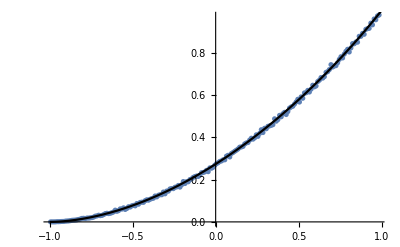

```mathematica
Show[
ListLinePlot[plotpoints[check[[5]],du,-1]],
ListPlot[plotpoints[ToExpression[majorant] Pi check[[6]],du,-1]],
Plot[ST`σ[u,ToExpression[roughness],ToExpression[gamma]],{u,-1,1},PlotStyle->Black]
]
```